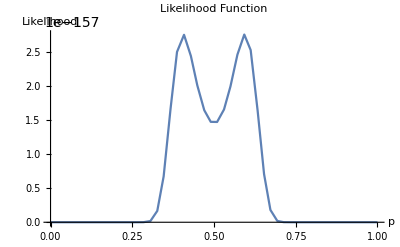

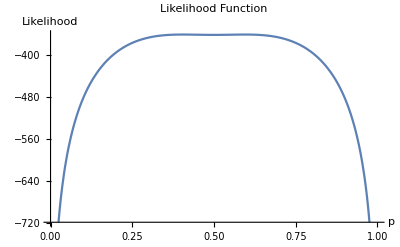

```mathematica
f[p_]:=(((p^4)+(1-p)^4)^21)*(((p^4) (1-p)+p (1-p)^4)^26)*(((p^4) ((1-p)^2)+(p^2) (1-p)^4)^24)*(((p^4) ((1-p)^3)+(p^3) (1-p)^4)^39);
graphic=Plot[f[p],{p,0,1},PlotLabel->"Likelihood Function",AxesLabel->{"p","Likelihood"}]
g[p_]:=Log10[(((p^4)+(1-p)^4)^21)*(((p^4) (1-p)+p (1-p)^4)^26)*(((p^4) ((1-p)^2)+(p^2) (1-p)^4)^24)*(((p^4) ((1-p)^3)+(p^3) (1-p)^4)^39)];
graphic=Plot[g[p],{p,0,1},PlotLabel->"Likelihood Function",AxesLabel->{"p","Likelihood"}]
```

```mathematica
N@ArgMax[{f[a],a>0.5},a]
```

0.595131

```mathematica
N@ArgMax[{g[a],a>0.5},a]
```

0.595131

```mathematica
Sum[Binomial[3+k,k]*0.41^k*0.59^4,{k,0,3}]
```

0.690619

```mathematica
Sum[Binomial[3+k,k]*0.41^k*0.59^4*k,{k,0,3}]+
Sum[Binomial[3+k,k]*0.59^k*0.41^4*k,{k,0,3}]
```

1.71882

```mathematica
N@(26+2*24+3*39)/110
```

1.73636

```mathematica
Solve[Sum[Binomial[3+k,k]*(1-p)^k*p^4*k,{k,0,3}]+
Sum[Binomial[3+k,k]*p^k*(1-p)^4*k,{k,0,3}]==1.7363636363636363,p]
```

{{p→-0.316484-0.308104 ⅈ},{p→-0.316484+0.308104 ⅈ},{p→0.418984},{p→0.581016},{p→1.31648-0.308104 ⅈ},{p→1.31648+0.308104 ⅈ}}